# WEEK-6_L-2

## ODE:

```mathematica
DSolve[{y'[x]==y[x]},y[x],x]
```

{{y[x]→ⅇ^x C[1]}}

```mathematica
y[x]/.DSolve[{y'[x]==y[x]},y[x],x]
```

{ⅇ^x C[1]}

```mathematica
sol=DSolve[{y'[x]==y[x],y[0]==1},y[x],x]
```

{{y[x]→ⅇ^x}}

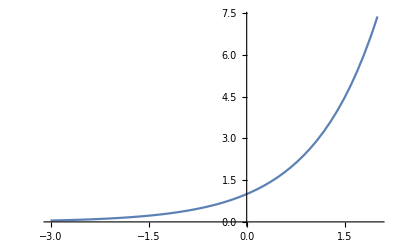

```mathematica
Plot[y[x]/.sol,{x,-3,2}]
```

```mathematica
s=NDSolve[{y'[x]==y[x],y[0]==1},y[x],{x,0,10}]
```

{{y[x]→InterpolatingFunction[…][x]}}

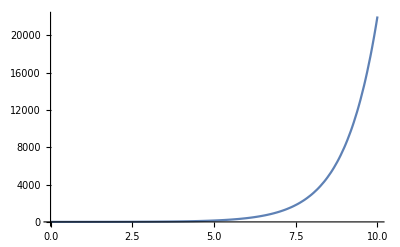

```mathematica
Plot[Evaluate[y[x]/.s],{x,0,10},PlotRange-> All]
```

```mathematica
eqn1={g'[y]==g[y]^2,g[0]==1};
```

```mathematica
sol1=DSolve[eqn1,g,y]
```

{{g→Function[{y},1/(1-y)]}}

```mathematica
DSolve[{f''[x]+5f'[x]+2*f[x]==0},f[x],x]
```

{{f[x]→ⅇ^((-5/2-(√17)/2) x) C[1]+ⅇ^((-5/2+(√17)/2) x) C[2]}}

```mathematica
DSolve[{f''[x]+5f'[x]+2*f[x]==0,f[0]==5,f'[0]==10},f[x],x]
```

{{f[x]→-5/34 (-17 ⅇ^((-5/2-(√17)/2) x)+9 √17 ⅇ^((-5/2-(√17)/2) x)-17 ⅇ^((-5/2+(√17)/2) x)-9 √17 ⅇ^((-5/2+(√17)/2) x))}}

```mathematica
a=NDSolve[{h''[x]+x*h[x]==0,h[0]==1,h[1]==1},h[x],{x,-5,10}]
```

{{h[x]→InterpolatingFunction[…][x]}}

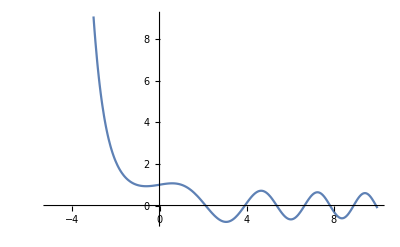

```mathematica
Plot[Evaluate[h[x]/.a],{x,-5,10}]
```

```mathematica
e=DSolve[{f''[x]+5f'[x]+2*f[x]==0},f[x],x]
```

{{f[x]→ⅇ^((-5/2-(√17)/2) x) C[1]+ⅇ^((-5/2+(√17)/2) x) C[2]}}

```mathematica
f=f[x]/.e[[1]]/.{C[1]-> 2,C[2] -> 3}
```

2 ⅇ^((-5/2-(√17)/2) x)+3 ⅇ^((-5/2+(√17)/2) x)

(ⅆ^2 y)/(ⅆ x^2)=z,  (ⅆ^2 z)/ⅆx=y where initial conditions are y(0)=0, y’(0)=0, and z(0)= -1,

```mathematica
sol=DSolve[{f''[x]=g[x],g'[x]=f[x],f[0]=1,f'[0]=0,g[0]=-1},{f,g},x];
```

Set::write: Tag Plus in (ⅇ^((-5/2-(√17)/2) x) 1+ⅇ^((-5/2+(√17)/2) x) 2)[0] is Protected.

DSolve::dsfun: ⅇ^((-5/2-(√17)/2) x) 1+ⅇ^((-5/2+(√17)/2) x) 2 cannot be used as a function.

```mathematica
y=f[x]/.Part[Part[sol,1],1]
```

ReplaceAll::reps: {x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(ⅇ^((-5/2-(√17)/2) x) C[1]+ⅇ^((-5/2+(√17)/2) x) C[2])[x]/.x

```mathematica
z=g[x]/.Part[Part[sol, 1],2]
```

ReplaceAll::reps: {(ⅇ^((-5/2-1/2 Power[«2»]) x) 1+ⅇ^((-5/2+1/2 Power[«2»]) x) 2)[x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.(ⅇ^((-5/2-(√17)/2) x) C[1]+ⅇ^((-5/2+(√17)/2) x) C[2])[x]

```mathematica
Solve[{m+n == 2*p, m-n == 2*q},{m,n}]
```

{{m→p+q,n→p-q}}

```mathematica
s=Solve[{m+n==2*p,m-n==2*q},{m,n}];
```

{{m→p+q,n→p-q}}

```mathematica
Part[s,1]
```

{m→p+q,n→p-q}

```mathematica
Part[Part[s,1],1]
```

m→p+q

```mathematica
Part[Part[s,1],2]
```

n→p-q